```mathematica
Animate[ParametricPlot[{Exp[-y] Cos[t - y],y},{y,0,10},PlotRange -> {{-1,1},{0,10}},AspectRatio -> 1/GoldenRatio,PlotStyle -> Thickness[0.01]],{t,0,2 π}]
```

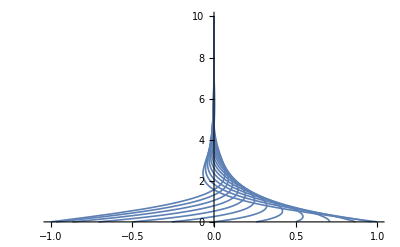

```mathematica
Show[
Table[ParametricPlot[{Exp[-y] Cos[t - y],y},{y,0,10},PlotRange -> {{-1,1},{0,10}},AspectRatio -> 1/GoldenRatio,PlotStyle -> Thickness[0.003]]
,{t,0, π,π/12}]
]
```